# Experiment 30B - Interaction of γ-rays with Matter

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"30b"]];
```

## Lead X-ray Fluorescence

### 2-point energy calibration using Cs-137 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/cs137.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.498
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	183.12
Live Time Elapsed:	151.45
Start Time:	05/17/2018 13:31:57
Stop Time:	05/17/2018 13:34:59

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

We find the channel locations of the 32 keV and 661.6 keV peaks and use the two data points to estimate correspondence between channel number and energy, assuming a linear correspondence over the entire spectrum, using the line equation E = (661.6 - 32)/(μ_661.6 - μ_32)(x - μ_661.6)+661.6 keV.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{19.77,31.44}

n= 12

4 points removed.

```mathematica
GaussianLFit[]
```

n = 12

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
5377.8 | d= 
251.153 |  | 
σ_c= 
1334.92 | σ_d= 
69.6569 |  | 
y_max= 
25332.4 | μ= 
24.9907 | sigma= 
4.05613 | 
σ_y_max= 
1521.73 | σ_μ= 
0.0697645 | σ_sigma= 
0.183934 | Std. deviation= 
185.69

Fit of (x,y±σ_y)

c= 
4886.39 | d= 
253.303 |  | 
σ_c= 
1105.5 | σ_d= 
54.7463 |  | 
y_max= 
25795.7 | μ= 
24.9905 | sigma= 
4.11778 | 
σ_y_max= 
1217.65 | σ_μ= 
0.0577911 | σ_sigma= 
0.149935 | χ^2/(n-5)= 
1.37424

Fit of (x±σ_x,y±σ_y)

c= 
4888.64 | d= 
253.284 |  | 
σ_c= 
1106.35 | σ_d= 
54.8234 |  | 
y_max= 
25793.6 | μ= 
24.9906 | sigma= 
4.11748 | 
σ_y_max= 
1218.95 | σ_μ= 
0.0578475 | σ_sigma= 
0.15007 | χ^2/(n-5)= 
1.37254

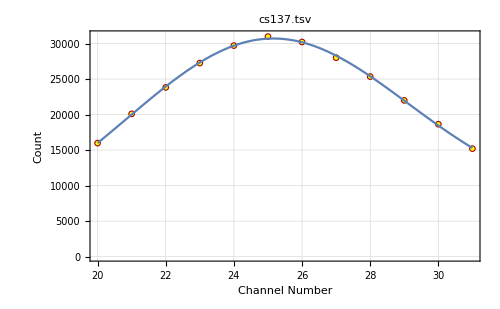
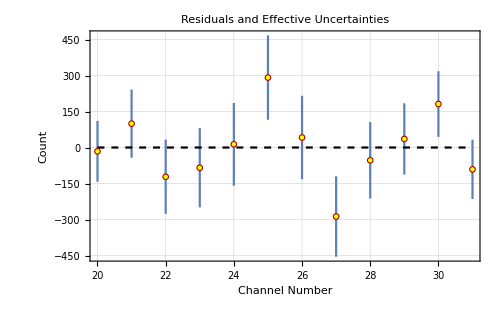
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
4888.64 | d= 
253.284 |  | 
σ_c= 
1106.35 | σ_d= 
54.8234 |  | 
y_max= 
25793.6 | μ= 
24.9906 | sigma= 
4.11748 | 
σ_y_max= 
1218.95 | σ_μ= 
0.0578475 | σ_sigma= 
0.15007 | χ^2/(n-5)= 
1.37254

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
x32={mean,sigmean}; (* channel number for 32 keV peak *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{761.3,811.14}

n= 50

18 points removed.

```mathematica
GaussianLFit[]
```

n = 68

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
909.422 | d= 
-22.8308 |  | 
σ_c= 
591.986 | σ_d= 
4.3578 |  | 
y_max= 
19418.1 | μ= 
787.147 | sigma= 
23.8036 | 
σ_y_max= 
621.424 | σ_μ= 
0.213775 | σ_sigma= 
0.562349 | Std. deviation= 
185.951

Fit of (x,y±σ_y)

c= 
769.566 | d= 
-22.1921 |  | 
σ_c= 
361.866 | σ_d= 
2.53895 |  | 
y_max= 
19548.9 | μ= 
787.114 | sigma= 
23.937 | 
σ_y_max= 
364.98 | σ_μ= 
0.134066 | σ_sigma= 
0.35789 | χ^2/(n-5)= 
2.04724

Fit of (x±σ_x,y±σ_y)

c= 
769.582 | d= 
-22.1922 |  | 
σ_c= 
361.886 | σ_d= 
2.53914 |  | 
y_max= 
19548.8 | μ= 
787.114 | sigma= 
23.937 | 
σ_y_max= 
365.004 | σ_μ= 
0.134073 | σ_sigma= 
0.357908 | χ^2/(n-5)= 
2.04713

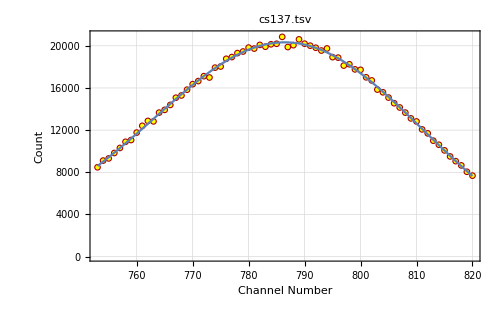
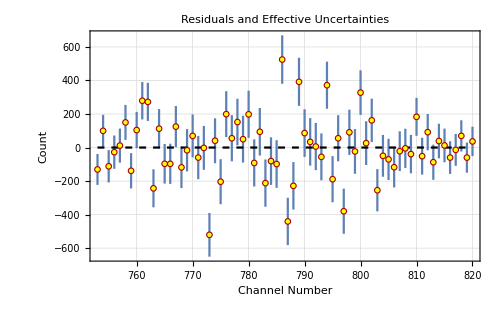
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
769.582 | d= 
-22.1922 |  | 
σ_c= 
361.886 | σ_d= 
2.53914 |  | 
y_max= 
19548.8 | μ= 
787.114 | sigma= 
23.937 | 
σ_y_max= 
365.004 | σ_μ= 
0.134073 | σ_sigma= 
0.357908 | χ^2/(n-5)= 
2.04713

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
x661={mean,sigmean}; (* channel number for 661.6 keV peak *)
```

```mathematica
(* We write a 2-point calibration function for our spectrum with error estimate: *)
```

```mathematica
cal1[channel_]:=((661.6-32)/(x661[[1]]-x32[[1]]) (channel[[1]]-x661[[1]])+661.6){1,Sqrt[(x661[[2]]^2+x32[[2]]^2)/(x661[[1]]-x32[[1]])^2+(x661[[2]]^2+channel[[2]]^2)/(channel[[1]]-x661[[1]])^2]};
```

### Estimating energy of lead X-ray fluorescence peak

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/lead_florescence.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.498
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	176.1
Live Time Elapsed:	150.56
Start Time:	05/17/2018 13:36:32
Stop Time:	05/17/2018 13:39:28

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

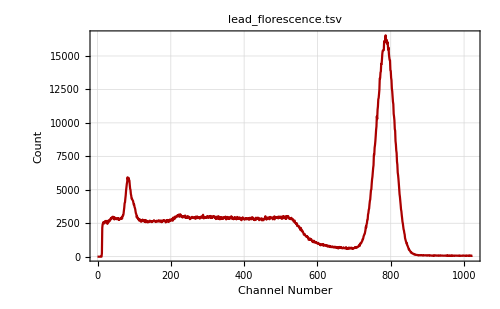

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{74.56,93.36}

n= 19

13 points removed.

```mathematica
GaussianLFit[]
```

n = 18

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
3126.38 | d= 
31.9012 |  | 
σ_c= 
283.612 | σ_d= 
10.7865 |  | 
y_max= 
2743.89 | μ= 
83.3242 | sigma= 
6.48827 | 
σ_y_max= 
401.242 | σ_μ= 
0.242177 | σ_sigma= 
0.442659 | Std. deviation= 
56.5519

Fit of (x,y±σ_y)

c= 
3136.95 | d= 
32.6801 |  | 
σ_c= 
329.983 | σ_d= 
13.4133 |  | 
y_max= 
2733.31 | μ= 
83.3008 | sigma= 
6.4635 | 
σ_y_max= 
509.033 | σ_μ= 
0.293283 | σ_sigma= 
0.889082 | χ^2/(n-5)= 
0.598447

Fit of (x±σ_x,y±σ_y)

c= 
3136.95 | d= 
32.6793 |  | 
σ_c= 
330.007 | σ_d= 
13.4154 |  | 
y_max= 
2733.31 | μ= 
83.3008 | sigma= 
6.46351 | 
σ_y_max= 
509.11 | σ_μ= 
0.29331 | σ_sigma= 
0.88919 | χ^2/(n-5)= 
0.598377

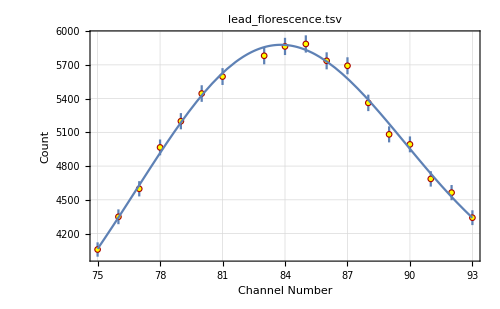
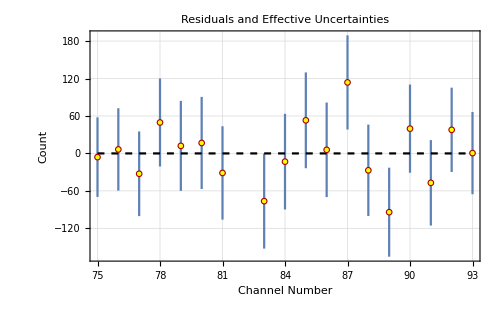
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
3136.95 | d= 
32.6793 |  | 
σ_c= 
330.007 | σ_d= 
13.4154 |  | 
y_max= 
2733.31 | μ= 
83.3008 | sigma= 
6.46351 | 
σ_y_max= 
509.11 | σ_μ= 
0.29331 | σ_sigma= 
0.88919 | χ^2/(n-5)= 
0.598377

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
flChannel={mean, sigmean};
```

```mathematica
cal1[flChannel]
```

{80.1709,0.0398179}

From the above, we can estimate the energy of the lead X-ray fluorescence peak to be 80.17 ± 0.04 keV.

## Thorium-232 Pair Production

We again assume a linear dependence of energy on channel count and construct a new calibration function for the detector settings used for the Cobalt-60 and Thorium 232 dataset.

```mathematica
(* We pull the Co-60 and Th-232 full energy peak channel counts for our calibration. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/co60_coincidence_peaks.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	650
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.546
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	635.6
Live Time Elapsed:	632.58
Start Time:	05/17/2018 14:13:11
Stop Time:	05/17/2018 14:23:47

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

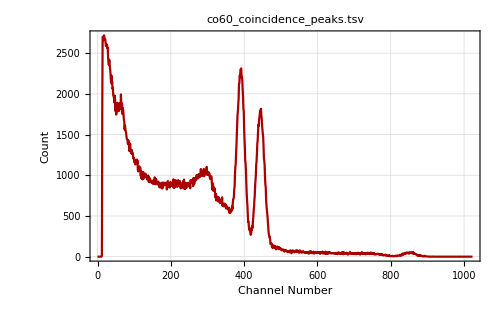

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{427.2,459.6}

n= 32

992 points removed.

```mathematica
GaussianLFit[]
```

n = 32

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
176.79 | d= 
0.0395994 |  | 
σ_c= 
113.94 | σ_d= 
1.98018 |  | 
y_max= 
1597.78 | μ= 
444.363 | sigma= 
10.9098 | 
σ_y_max= 
136.125 | σ_μ= 
0.24533 | σ_sigma= 
0.70576 | Std. deviation= 
28.0404

Fit of (x,y±σ_y)

c= 
177.188 | d= 
0.280654 |  | 
σ_c= 
131.495 | σ_d= 
2.28744 |  | 
y_max= 
1596.78 | μ= 
444.328 | sigma= 
10.9082 | 
σ_y_max= 
160.684 | σ_μ= 
0.299839 | σ_sigma= 
0.858511 | χ^2/(n-5)= 
0.582677

Fit of (x±σ_x,y±σ_y)

c= 
177.187 | d= 
0.280333 |  | 
σ_c= 
131.504 | σ_d= 
2.28792 |  | 
y_max= 
1596.78 | μ= 
444.328 | sigma= 
10.9082 | 
σ_y_max= 
160.773 | σ_μ= 
0.299899 | σ_sigma= 
0.85892 | χ^2/(n-5)= 
0.582479

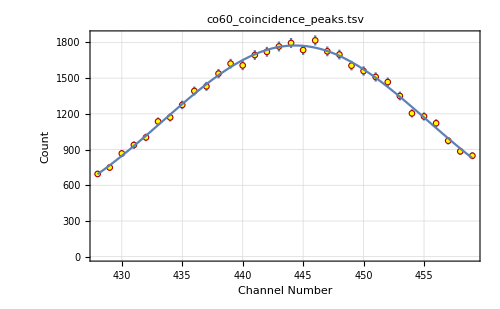
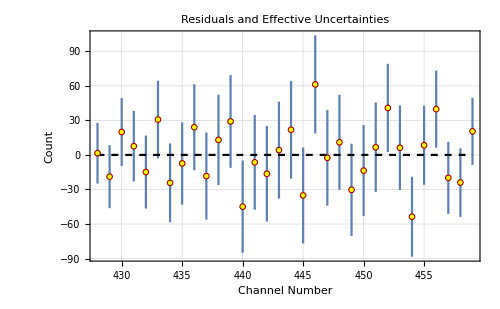
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
177.187 | d= 
0.280333 |  | 
σ_c= 
131.504 | σ_d= 
2.28792 |  | 
y_max= 
1596.78 | μ= 
444.328 | sigma= 
10.9082 | 
σ_y_max= 
160.773 | σ_μ= 
0.299899 | σ_sigma= 
0.85892 | χ^2/(n-5)= 
0.582479

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
co133={1.332,mean,sigmean};
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{375.,405.6}

n= 31

993 points removed.

```mathematica
GaussianLFit[]
```

n = 31

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
408.374 | d= 
-7.26172 |  | 
σ_c= 
113.801 | σ_d= 
2.62444 |  | 
y_max= 
1883.71 | μ= 
391.202 | sigma= 
9.81801 | 
σ_y_max= 
128.753 | σ_μ= 
0.239165 | σ_sigma= 
0.426457 | Std. deviation= 
35.4693

Fit of (x,y±σ_y)

c= 
451.308 | d= 
-6.10671 |  | 
σ_c= 
110.044 | σ_d= 
2.59049 |  | 
y_max= 
1843.16 | μ= 
391.091 | sigma= 
9.64415 | 
σ_y_max= 
126.05 | σ_μ= 
0.223341 | σ_sigma= 
0.571047 | χ^2/(n-5)= 
0.765305

Fit of (x±σ_x,y±σ_y)

c= 
451.238 | d= 
-6.10821 |  | 
σ_c= 
110.086 | σ_d= 
2.5918 |  | 
y_max= 
1843.23 | μ= 
391.091 | sigma= 
9.64444 | 
σ_y_max= 
126.119 | σ_μ= 
0.223392 | σ_sigma= 
0.571286 | χ^2/(n-5)= 
0.765

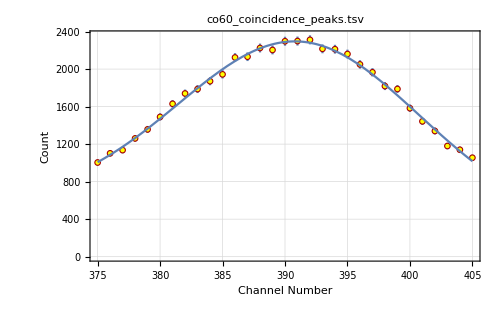
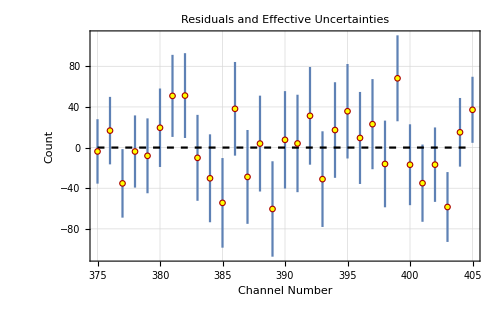
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
451.238 | d= 
-6.10821 |  | 
σ_c= 
110.086 | σ_d= 
2.5918 |  | 
y_max= 
1843.23 | μ= 
391.091 | sigma= 
9.64444 | 
σ_y_max= 
126.119 | σ_μ= 
0.223392 | σ_sigma= 
0.571286 | χ^2/(n-5)= 
0.765

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
co117={1.173,mean,sigmean};
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/pair_production_thorium.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	650
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.546
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	557.97
Live Time Elapsed:	530.1
Start Time:	05/17/2018 14:28:31
Stop Time:	05/17/2018 14:37:48

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

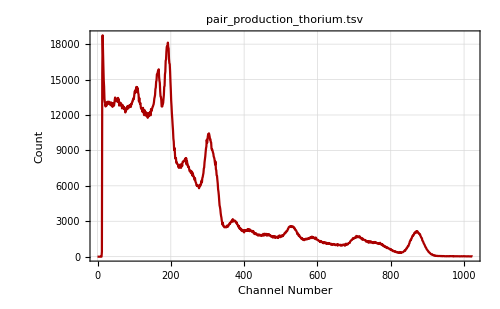

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{840.2,899.6}

n= 59

965 points removed.

```mathematica
GaussianLFit[]
```

n = 59

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
140.281 | d= 
-1.64323 |  | 
σ_c= 
55.9298 | σ_d= 
0.707084 |  | 
y_max= 
1968.39 | μ= 
870.911 | sigma= 
16.8912 | 
σ_y_max= 
57.6184 | σ_μ= 
0.209188 | σ_sigma= 
0.461354 | Std. deviation= 
34.9043

Fit of (x,y±σ_y)

c= 
168.246 | d= 
-1.58702 |  | 
σ_c= 
47.7163 | σ_d= 
0.602506 |  | 
y_max= 
1942.84 | μ= 
870.904 | sigma= 
16.6605 | 
σ_y_max= 
46.753 | σ_μ= 
0.209728 | σ_sigma= 
0.426278 | χ^2/(n-5)= 
0.843824

Fit of (x±σ_x,y±σ_y)

c= 
168.233 | d= 
-1.58703 |  | 
σ_c= 
47.725 | σ_d= 
0.602624 |  | 
y_max= 
1942.85 | μ= 
870.904 | sigma= 
16.6606 | 
σ_y_max= 
46.7638 | σ_μ= 
0.209758 | σ_sigma= 
0.419356 | χ^2/(n-5)= 
0.843657

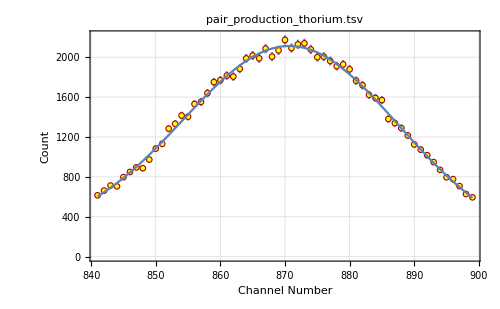
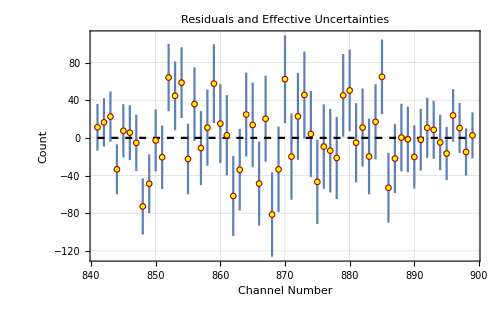
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
168.233 | d= 
-1.58703 |  | 
σ_c= 
47.725 | σ_d= 
0.602624 |  | 
y_max= 
1942.85 | μ= 
870.904 | sigma= 
16.6606 | 
σ_y_max= 
46.7638 | σ_μ= 
0.209758 | σ_sigma= 
0.419356 | χ^2/(n-5)= 
0.843657

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
th261={2.61,mean,sigmean};
```

### Constructing the calibration function

```mathematica
Export["calData.dat",Partition[Join[co117,co133,th261],3]];
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/calData.dat

Read 3 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 3

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.00108841 | b= 
0.00299593 | 
σ_a= 
0.000573183 | σ_b= 
9.42864×10^-7 | Std. deviation= 
0.000350509

Fit of (x±σ_x,y±σ_y)

a= 
0.00121159 | b= 
0.00299579 | 
σ_a= 
0.00117895 | σ_b= 
1.88276×10^-6 | χ^2/(n-2)= 
0.189787

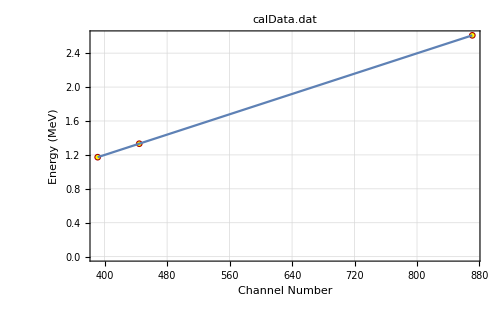
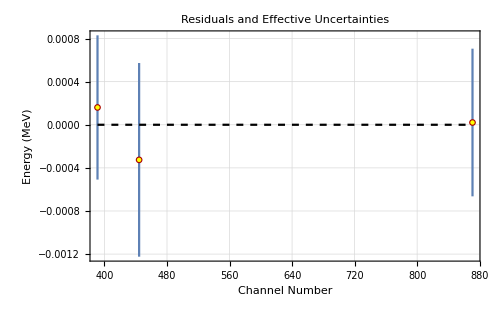
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.00121159 | b= 
0.00299579 | 
σ_a= 
0.00117895 | σ_b= 
1.88276×10^-6 | χ^2/(n-2)= 
0.189787

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Energy (MeV)"}]
```

Since we will be using this calibration function to measure energy spacings, we do not have to concern ourselves with the offset a.

```mathematica
scaling={b,sigb};
```

```mathematica
cal2[spacing_]:=scaling[[1]] spacing[[1]]{1,Sqrt[(scaling[[2]]/scaling[[1]])^2+(spacing[[2]]/spacing[[1]])^2]};
```

```mathematica
spacing[escPeak_]:={th261[[2]]-escPeak[[1]],Sqrt[th261[[3]]^2+escPeak[[2]]^2]};
```

### Spacing between full-energy peak and escape peaks

#### One-escape peak

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/pair_production_thorium.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	650
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.546
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	557.97
Live Time Elapsed:	530.1
Start Time:	05/17/2018 14:28:31
Stop Time:	05/17/2018 14:37:48

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{690.6,731.2}

n= 41

983 points removed.

```mathematica
GaussianLFit[]
```

n = 38

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1294.19 | d= 
1.04966 |  | 
σ_c= 
43.2556 | σ_d= 
1.19459 |  | 
y_max= 
395.347 | μ= 
709.71 | sigma= 
11.0849 | 
σ_y_max= 
67.2199 | σ_μ= 
0.687887 | σ_sigma= 
1.23682 | Std. deviation= 
30.0481

Fit of (x,y±σ_y)

c= 
1291.43 | d= 
1.14833 |  | 
σ_c= 
53.5445 | σ_d= 
1.67359 |  | 
y_max= 
397.158 | μ= 
709.626 | sigma= 
11.1475 | 
σ_y_max= 
98.4556 | σ_μ= 
0.897563 | σ_sigma= 
2.48909 | χ^2/(n-5)= 
0.574592

Fit of (x±σ_x,y±σ_y)

c= 
1291.43 | d= 
1.14832 |  | 
σ_c= 
53.5445 | σ_d= 
1.6736 |  | 
y_max= 
397.158 | μ= 
709.626 | sigma= 
11.1475 | 
σ_y_max= 
98.4558 | σ_μ= 
0.897566 | σ_sigma= 
2.48909 | χ^2/(n-5)= 
0.574586

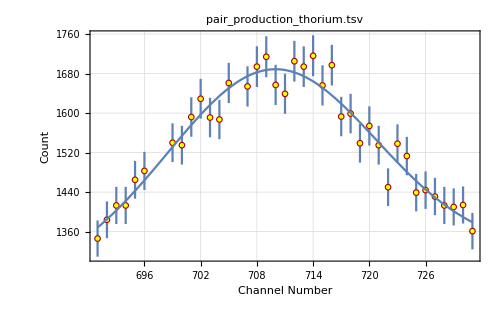
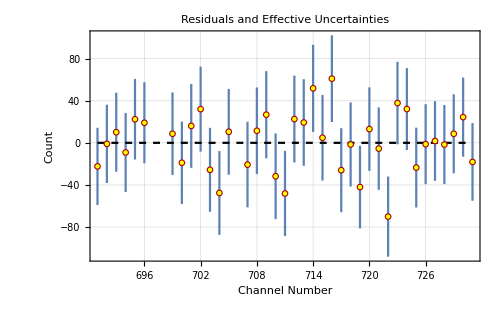
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
1291.43 | d= 
1.14832 |  | 
σ_c= 
53.5445 | σ_d= 
1.6736 |  | 
y_max= 
397.158 | μ= 
709.626 | sigma= 
11.1475 | 
σ_y_max= 
98.4558 | σ_μ= 
0.897566 | σ_sigma= 
2.48909 | χ^2/(n-5)= 
0.574586

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
oneEsc=spacing[{mean,sigmean}];
```

```mathematica
cal2[oneEsc]
```

{0.482874,0.00279134}

Therefore, using the one-escape peak, we estimate an electron rest mass energy m_e=0.4829 ± 0.0028 MeV.

#### Two-escape peak

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/pair_production_thorium.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	650
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.546
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	557.97
Live Time Elapsed:	530.1
Start Time:	05/17/2018 14:28:31
Stop Time:	05/17/2018 14:37:48

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{511.2,553.8}

n= 42

982 points removed.

```mathematica
GaussianLFit[]
```

n = 42

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1352.79 | d= 
-0.33994 |  | 
σ_c= 
147.607 | σ_d= 
2.43479 |  | 
y_max= 
1229.94 | μ= 
529.134 | sigma= 
14.4207 | 
σ_y_max= 
208.12 | σ_μ= 
0.652027 | σ_sigma= 
1.64351 | Std. deviation= 
38.9917

Fit of (x,y±σ_y)

c= 
1352.63 | d= 
-0.342961 |  | 
σ_c= 
187.129 | σ_d= 
3.16705 |  | 
y_max= 
1229.91 | μ= 
529.133 | sigma= 
14.4087 | 
σ_y_max= 
217.456 | σ_μ= 
0.867393 | σ_sigma= 
1.74187 | χ^2/(n-5)= 
0.712248

Fit of (x±σ_x,y±σ_y)

c= 
1352.63 | d= 
-0.342994 |  | 
σ_c= 
187.125 | σ_d= 
3.16697 |  | 
y_max= 
1229.91 | μ= 
529.133 | sigma= 
14.4087 | 
σ_y_max= 
217.48 | σ_μ= 
0.867373 | σ_sigma= 
1.74202 | χ^2/(n-5)= 
0.71222

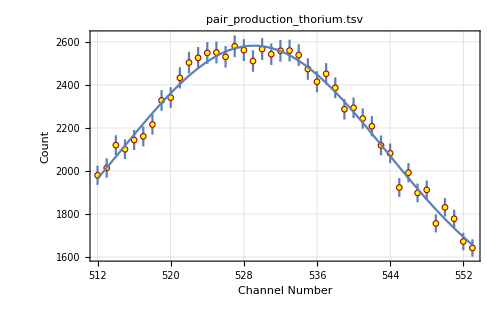
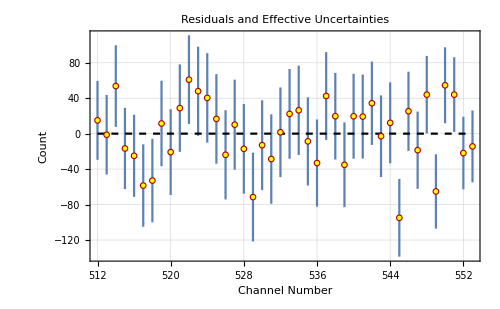
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
1352.63 | d= 
-0.342994 |  | 
σ_c= 
187.125 | σ_d= 
3.16697 |  | 
y_max= 
1229.91 | μ= 
529.133 | sigma= 
14.4087 | 
σ_y_max= 
217.48 | σ_μ= 
0.867373 | σ_sigma= 
1.74202 | χ^2/(n-5)= 
0.71222

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

```mathematica
twoEsc=spacing[{mean,sigmean}];
```

```mathematica
cal2[twoEsc]/2
```

{0.511797,0.00138158}

Therefore, using the one-escape peak, we estimate an electron rest mass energy m_e=0.5118± 0.0014 MeV.

### Comments

We observe that we obtain a much better estimate of m_e using the two-escape peak than using the one-escape peak (in fact we are within error of the NIST value whereas the one-escape peak estimate is >5σ off).

## Plastic Scintillator

### Cs-137 NaI Scintillator

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/cs137_encore_ref.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.432
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	702.26
Live Time Elapsed:	571.89
Start Time:	05/17/2018 14:45:01
Stop Time:	05/17/2018 14:56:43

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{369.,653.2}

n= 285

739 points removed.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

285 Y count values have had sigma values assigned.

285 X channel values have had sigma values assigned.

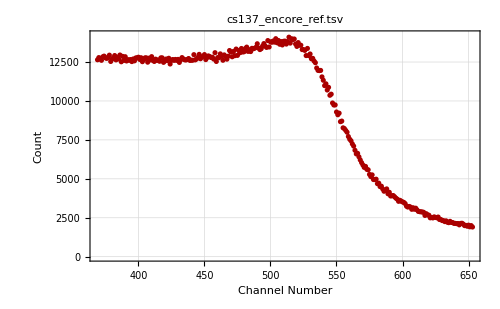

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"}]
```

### Cs-137 Plastic Scintillator

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_cs137.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.696
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	484.5
Live Time Elapsed:	463.7
Start Time:	05/17/2018 15:08:19
Stop Time:	05/17/2018 15:16:24

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{287.2,728.2}

n= 441

583 points removed.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

441 Y count values have had sigma values assigned.

441 X channel values have had sigma values assigned.

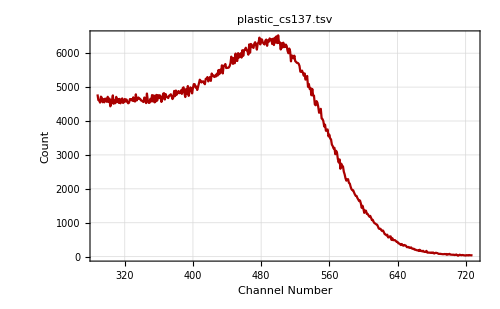

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"}]
```

The plastic scintillator Compton edge is much more pronounced, and appears as a discernible peak. The peak also appears slightly shifted towards lower energies for the plastic scintillator.

### Estimating mean number of photoelectrons generated by 661.6 keV detection - NaI detector

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/cs137_encore_ref.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.432
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	702.26
Live Time Elapsed:	571.89
Start Time:	05/17/2018 14:45:01
Stop Time:	05/17/2018 14:56:43

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{750.,814.8}

n= 65

959 points removed.

```mathematica
GaussianLFit[]
```

n = 65

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
5177.01 | d= 
-78.8056 |  | 
σ_c= 
1841.21 | σ_d= 
14.1724 |  | 
y_max= 
79308.4 | μ= 
782.623 | sigma= 
23.5197 | 
σ_y_max= 
2128.52 | σ_μ= 
0.152089 | σ_sigma= 
0.460947 | Std. deviation= 
518.167

Fit of (x,y±σ_y)

c= 
5184.42 | d= 
-77.033 |  | 
σ_c= 
873.314 | σ_d= 
5.98608 |  | 
y_max= 
79301.8 | μ= 
782.594 | sigma= 
23.5151 | 
σ_y_max= 
841.626 | σ_μ= 
0.0728649 | σ_sigma= 
0.19376 | χ^2/(n-5)= 
3.91897

Fit of (x±σ_x,y±σ_y)

c= 
5184.42 | d= 
-77.0335 |  | 
σ_c= 
873.285 | σ_d= 
5.98655 |  | 
y_max= 
79301.8 | μ= 
782.594 | sigma= 
23.5151 | 
σ_y_max= 
841.754 | σ_μ= 
0.0728689 | σ_sigma= 
0.193784 | χ^2/(n-5)= 
3.91872

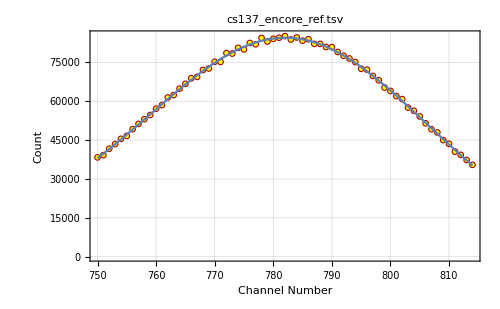
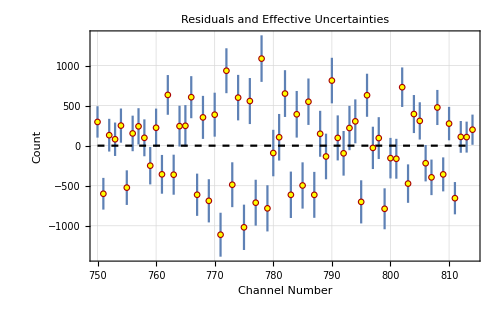
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
5184.42 | d= 
-77.0335 |  | 
σ_c= 
873.285 | σ_d= 
5.98655 |  | 
y_max= 
79301.8 | μ= 
782.594 | sigma= 
23.5151 | 
σ_y_max= 
841.754 | σ_μ= 
0.0728689 | σ_sigma= 
0.193784 | χ^2/(n-5)= 
3.91872

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number", "Count"}]
```

From equation (30.C.2) in the lab manual, derived from basic Poisson statistics, we can estimate the mean number of photoelectrons generated by a 661.6 MeV detection by the variance of the full-energy peak:

```mathematica
photoelectrons={sigma^2,2 sigsigma sigma}
```

{552.958,9.11371}

That is, the mean number of photoelectrons generated by a 661.6 MeV detection is 553 ± 9. We can then use the definition of μ in Appendix C (alternatively, equation (30.C.6)) to estimate E_pe, the energy per photoelectron. We use as in the pre-lab (σ(bin))/(μ(bin))=(σ(T_e))/T_e.

Note: Even if there is an offset in the calibration (so far all calibrations have had offset consistent with 0), the expression is adequate since we are at a channel number far enough from 0.

```mathematica
Epe=(661.6 photoelectrons[[1]])/mean^2{1,Sqrt[(photoelectrons[[2]]/photoelectrons[[1]])^2+((2 sigmean)/mean)^2]}
```

{0.597331,0.00984567}

and we estimate E_pe=597 ± 10 eV.

### Estimating mean number of photoelectrons generated by 661.6 keV detection - Plastic detector

Here we cannot use the approach described above, as our spectrum for the plastic scintillator contains no full-energy peak. We first attempt to manually vary the parameter E_pe in the Compton_Spectra1.nb provided until we obtain a Compton edge that appears to fit our data.

#### Cs-137 Compton edge for plastic scintillator

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_cs137.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.696
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	484.5
Live Time Elapsed:	463.7
Start Time:	05/17/2018 15:08:19
Stop Time:	05/17/2018 15:16:24

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

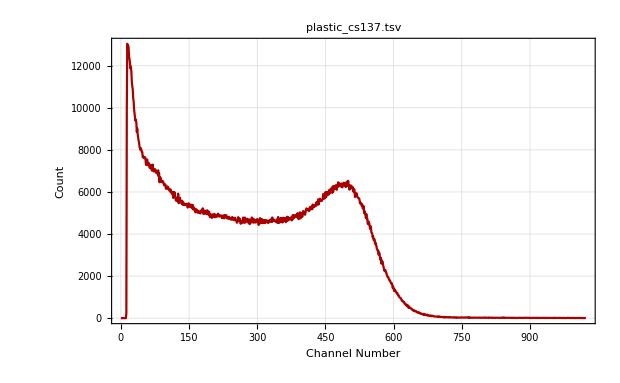

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number", "Count"},ImageSize->620]
```

#### Cs-137 Compton edge model for E_pe=2 keV

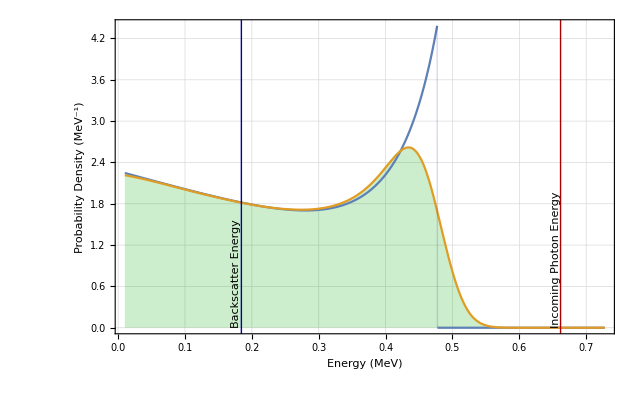

The model appears qualitatively similar to our Compton edge data (reproduced above for comparison) at E_pe≈ 2 MeV.

### Fit of Cs-137 Compton edge for plastic scintillator

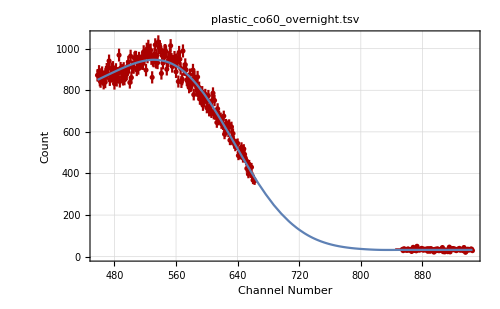
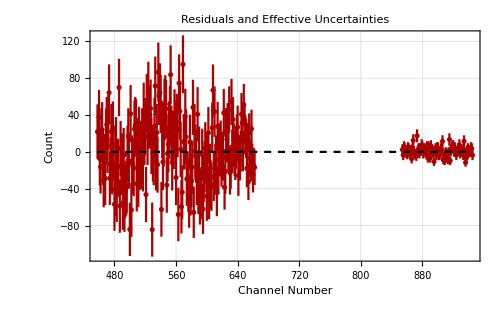
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
5846.36 | sigEPE = 
147.789 | 
Xscale (channels/MeV) = 
1299.2 | sigXscale = 
1.0572 | 
Yscale = 
(counts/channel)/(probability/MeV)
413.836 | sigYscale = 
1.84396 | 
Yoffset (counts/channel) = 
32.57 | sigYoffset = 
0.594918 | 
Xedge (channel) = 
620.083 | sigXedge = 
0.504581 | χ^2 = 
1.26291

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

From this we obtain an estimate of E_pe=5.85 ± 0.15 keV.

#### Cs-137 Compton edge model for E_pe=5.846keV

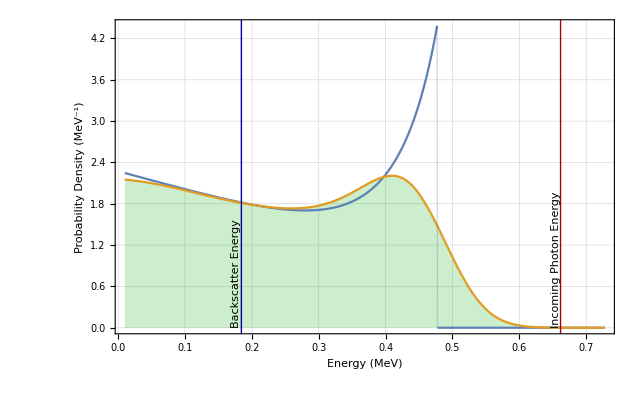

We plot the Compton edge model for E_pe matching the fit parameter obtained above. Interestingly, we observe that the model generated qualitatively appears to be less similar to our Compton edge data outside of a very small region around the Compton edge than our initial guess of 2 keV (which we know is typical of plastic scintillators). However, attempting to remedy this by fitting a larger section of the data significantly worsens the fit:

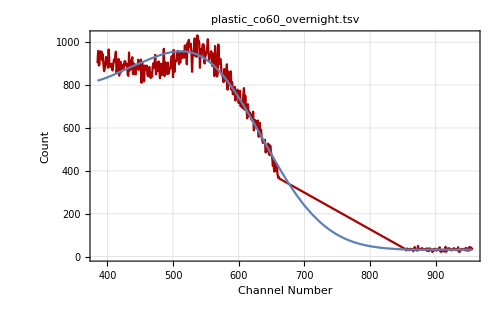
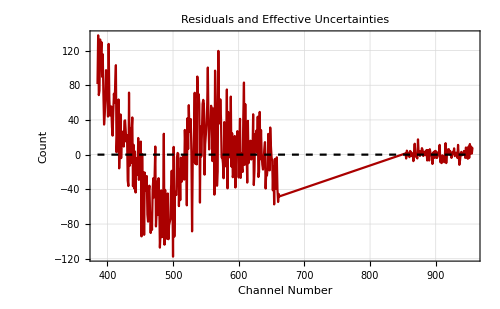
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
8327.61 | sigEPE = 
162.84 | 
Xscale (channels/MeV) = 
1292.4 | sigXscale = 
1.15018 | 
Yscale = 
(counts/channel)/(probability/MeV)
443.216 | sigYscale = 
1.35316 | 
Yoffset (counts/channel) = 
32.7521 | sigYoffset = 
0.56615 | 
Xedge (channel) = 
616.837 | sigXedge = 
0.548961 | χ^2 = 
2.29648

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

This indicates that the Compton edge model we are fitting against does not adequately describe our measurements, at least outside a narrow region around the Compton edge. For instance, the count drops much faster than expected right before the Compton edge. This could be due to other effects that become significant at lower energies (we know such effects exist due to the observed dramatic count increase at low energies observed on the full Cs-137 plastic scintillator spectrum, although we do not know at what energies those effects become significant or how they affect the spectrum outside of the very low-energy region).